### Energy spectrum of the split electron box

```mathematica
Remove["Global`*"]
```

ng: gate charge CgU/2e, 0<ng<0.49999 
ib: band index, 1 = ground
g=Ej/Ec (Ej of box, Ec of 2 electrons)
en : energy in units of Ec

```mathematica
en[ng_,ib_,g_,δ_,d_]:=Block[{gprim=g Sqrt[(1+d^2+(1-d^2)Cos[δ])/2]},MathieuCharacteristicA[ib-Mod[ib,2]-2(-1)^ib ng,-2 gprim]/4]
enn[ng_,ib_,g_,δ_,d_] := Piecewise[{{en[ng,ib,g,δ,d],And[ng>0,ng <0.5]},{en[1.0-ng,ib,g,δ,d],ng>=0.5}}]
in[ng_,ib_,g_,δ_,d_]:=-(en[ng,ib,g,δ+.01,d]-en[ng,ib,g,δ-.01,d])/.02/g
```

```mathematica
plenng[ib_,g_,δ_,d_,opts___]:=Plot[en[ng,ib,g,δ,d],{ng,0,0.4999},opts]
```

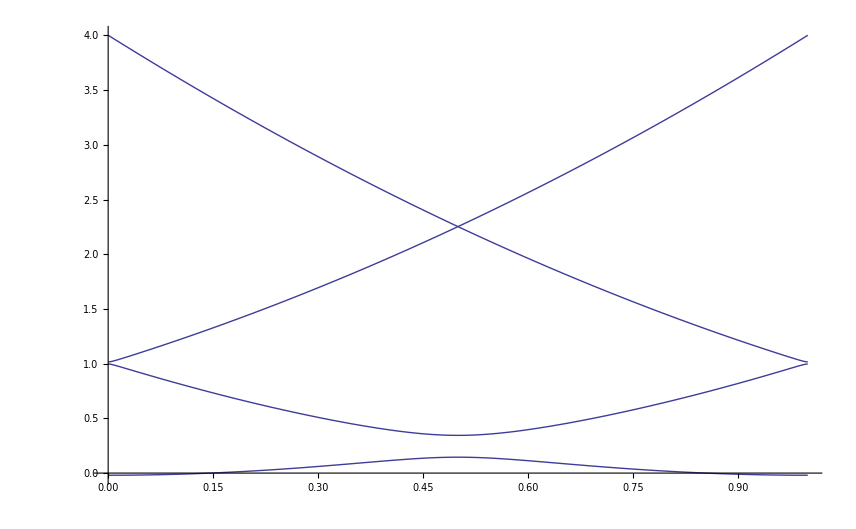

```mathematica
Plot[{enn[ng,1,g,δ,d],enn[ng,2,g,δ,d],enn[ng,3,g,δ,d],enn[ng,4,g,δ,d]} /. {g->0.2,d->0.,δ->0.},{ng,0,1},PlotRange->Full]
```

```mathematica
Map[Block[{gv=#},Export[NotebookDirectory[]<>"cpb_levels_g="<>ToString[gv]<>".csv",Map[{#,enn[ng,1,g,δ,d],enn[ng,2,g,δ,d],enn[ng,3,g,δ,d],enn[ng,4,g,δ,d]} /. {g->gv,d->0.,δ->0.,ng->#}&,Range[0,1,0.001]]]]&,{0.25,0.5,1,2,4,8}]
```

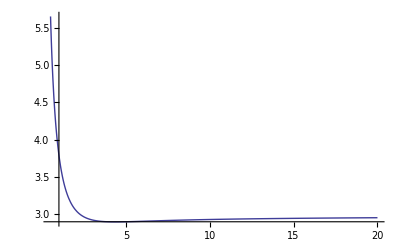

```mathematica
Plot[(enn[ng,2,g,δ,d]+enn[ng,3,g,δ,d]-2 enn[ng,1,g,δ,d])/(enn[ng,2,g,δ,d]-enn[ng,1,g,δ,d])/. {d->0,δ->0,ng->0.4999},{g,0.5,20},PlotRange->Full]
```

```mathematica
enn[ng,2,g,δ,d]-enn[ng,1,g,δ,d]/. {d->0,δ->0,ng->0.499999,g->1}
```

0.942469

```mathematica
Export[NotebookDirectory[]<>"cpb_relative_anharmonicity_ng=0_5.csv",Map[{#,(enn[ng,2,g,δ,d]+enn[ng,3,g,δ,d]-2 enn[ng,1,g,δ,d])/(enn[ng,2,g,δ,d]-enn[ng,1,g,δ,d])} /. {g->#,d->0.,δ->0.,ng->0.4999}&,Range[0.5,20.,0.01]]]
```

E:\cygwin\home\adewes\thesis\material\mathematica\cpb_relative_anharmonicity_ng=0_5.csv

```mathematica
dedn = D[enn[ng,2,g,δ,d]-enn[ng,1,g,δ,d],{ng,2}];
```

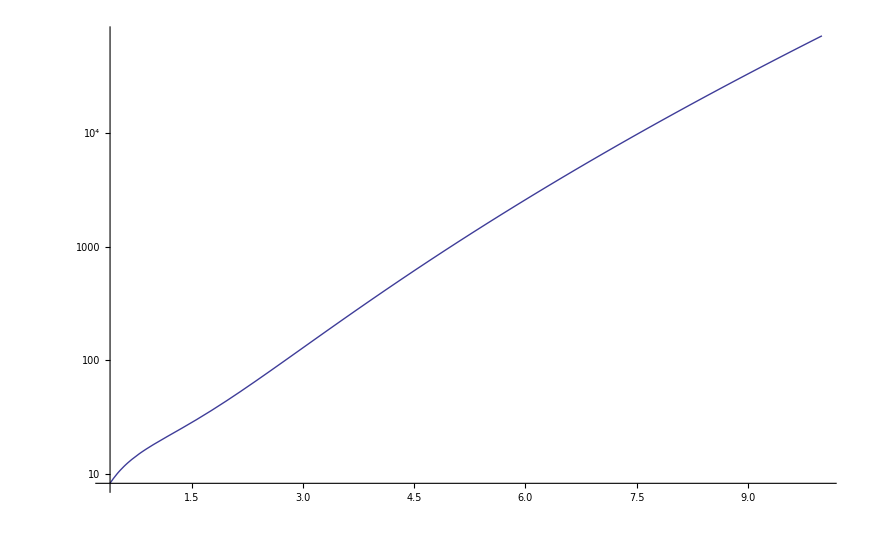

```mathematica
LogPlot[1/dedn /. {δ->0,d->0,ng->0.4999},{g,0.4,10}]
```